# Tight Binding in Graphene

Before moving to the method, let’s study how Graphene is formed:

Graphene is an arrangement of Carbon atoms in a 2D honeycomb lattice.

The electronic configuration is

C: 1s^2 2s^22p^2

Only the 2s and 2p orbitals participate in bonding; therefore, 4 valence electrons.

In the 2D honeycomb structure, each carbon atom:

Carbon has one 2s and three 2p orbitals: 

In sp.b2 hybridization, the atom mixes 2s, 2p_x, and 2p_y → forming three equivalent sp.b2 orbitals (because each atom is bonding to three atoms)

These lie in the xy-plane and are oriented 120° apart

The remaining 2p_z orbital is unchanged, perpendicular to the plane. Is this pz orbital empty? well, no, is forming a bond:

In the ground state electrons in carbon are distributed as:

| Orbital | Electrons |
| ------- | --------- |
| 2s      | ↑↓        |
| 2px   | ↑         |
| 2py   | ↑         |
| 2pz   | (empty)   |

As is here, this will allow just two bonds, not three, so carbon promote one electron from 2s -> 2pz.

| Orbital | Electrons |
| ------- | --------- |
| 2s      | ↑         |
| 2p\_x   | ↑         |
| 2p\_y   | ↑         |
| 2p\_z   | ↑         |

Now it has 3 unpaired electrons  in the 3sp2 hybridization— ready to make 3 bonds with the three neighboors

Why 3 sp2 hybridization? each with one electron?  If I start in a 3D orbital space (2s, 2pₓ, 2pᵧ), then any combination still lives in that 3D space. So the number of independent orbitals doesn’t change — just their form and orientation.

-The electron must still live in the same Hilbert space (here, spanned by 2s, 2pₓ, 2pᵧ).
-You’re just creating better orbitals to describe bonding — aligned with nuclei.
-You get 3 new hybrid orbitals (sp.b2) because you started with 3 linearly independent orbitals.

Now each carbon forms:

3 sp.b2 hybrid orbitals → each contains 1 unpaired electron

Leaves the pz orbital unhybridized, with 1 unpaired electron too

Forms 3 σ-bonds with neighboring atoms via sp.b2 orbitals (1 electron from each atom → 2 in the bond)

The remaining pz electron overlaps with neighboring pz orbitals → π bonding

         π cloud
        ↑     ↑
      C—C—C—C—C     ← sp.b2 σ-bonds in-plane
        ↓     ↓
         π cloud

Each orbital becomes fully occupied (↑↓) after bonding.

The blue arrows form strong σ-bonds with neighbors

In the following plot is illustrated the directions of this bonds. Red arrow overlaps with pz​ orbitals from other atoms above and below the plane → π-bonds

```mathematica
Graphics3D[{Arrowheads[0.05],Blue,Arrow[{{0,0,0},{1,0,0}}],(*sp.b2 1*)Arrow[{{0,0,0},{-1/2,Sqrt[3]/2,0}}],(*sp.b2 2*)Arrow[{{0,0,0},{-1/2,-Sqrt[3]/2,0}}],(*sp.b2 3*)Red,Arrow[{{0,0,0},{0,0,1}}]  (*remaining pz orbital*)},Boxed->False,Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"x","y","z"},PlotRange->{{-1,1},{-1,1},{0,1.2}}]
```

-Graphics3D-

The lobe that is created from a centered carbon atom can be visualize:

​

The bond, is the superposition of the hybrid orbitals (2 sp2 directed in opposite direction).

I will plot the sp2 bond betwwen two carbon atoms, i took a lot of time because i tried in spherical coordinates and make sure wavefunctions were normalized, it was confusing bc i am using IA and you can not trust it, so at the end i could do it, hopefully is correct.

```mathematica
Quit
```

```mathematica
(*Load hydrogenic orbital function*)
ψ=ResourceFunction["HydrogenWavefunction"];
Zeff=3.25;
θFixed=Pi/2;
```

```mathematica
(*sp.b2 orbital pointing at angle φ₀*)
ψsp2Angle[r_,θ_,ϕ_,φ0_]:=Module[
{ψs,ψp1,ψpm1,ψpx,φRot},
φRot=ϕ-φ0;
ψs=ψ[{2,0,0},Zeff,{r,θ,φRot}];
ψp1=ψ[{2,1,-1},Zeff,{r,θ,φRot}];
ψpm1=ψ[{2,1,1},Zeff,{r,θ,φRot}];
ψpx=(ψpm1-ψp1)/Sqrt[2];
(1/Sqrt[3]) ψs+Sqrt[2/3] ψpx];
```

```mathematica
ψ1[x_,y_,z_]:=Module[
{R0,α,x1,y1,z1,r1,ϕ1,θ1},
R0=3.0;
α=Pi;
x1=-R0;y1=0;z1=0;(*Atom A*)
r1=Sqrt[(x-x1)^2+(y-y1)^2+(z-z1)^2]+10^-6;
ϕ1=ArcTan[x-x1,y-y1];
θ1=ArcCos[(z-z1)/r1];
ψsp2Angle[r1,θ1,ϕ1,0]];
```

```mathematica
normalization1=NIntegrate[Abs[ψ1[x,y,z]]^2,{x,-10,10},{y,-10,10},{z,-10,10},Method->"AdaptiveMonteCarlo",AccuracyGoal->3,PrecisionGoal->3]
```

0.331716

```mathematica
(*Correct normalization*)
ψ1Norm[x_,y_,z_]:=ψ1[x,y,z]/Sqrt[normalization1]

(*Now check normalization*)
NIntegrate[Abs[ψ1Norm[x,y,z]]^2,{x,-10,10},{y,-10,10},{z,-10,10},Method->"AdaptiveMonteCarlo",AccuracyGoal->3,PrecisionGoal->3]
```

0.999308

```mathematica
(*atom at x=-3, one sp2 hybrid orbita;*)
```

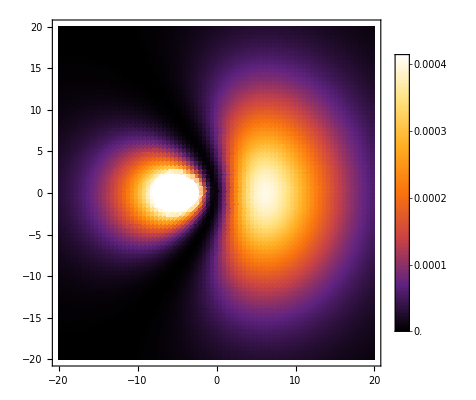

```mathematica
DensityPlot[Abs[ψ1Norm[x,y,0]]^2,{x,-20,20},{y,-20,20},PlotPoints->80,ColorFunction->"SunsetColors",PlotLegends->Automatic,Exclusions->None]
```

```mathematica
ψ2[x_,y_,z_]:=Module[
{R0,α,x2,y2,z2,r2,ϕ2,θ2},
R0=3.0;
α=Pi;
x2=R0;y2=0;z2=0;(*Atom B*)
r2=Sqrt[(x-x2)^2+(y-y2)^2+(z-z2)^2]+10^-6;
ϕ2=ArcTan[x-x2,y-y2];
θ2=ArcCos[(z-z2)/r2];
ψsp2Angle[r2,θ2,ϕ2,Pi]];
```

```mathematica
normalization2=NIntegrate[Abs[ψ2[x,y,z]]^2,{x,-10,10},{y,-10,10},{z,-10,10},Method->"AdaptiveMonteCarlo",AccuracyGoal->3,PrecisionGoal->3]
```

0.33167

```mathematica
(*Correct normalization*)
ψ2Norm[x_,y_,z_]:=ψ2[x,y,z]/Sqrt[normalization2]

(*Now check normalization*)
NIntegrate[Abs[ψ2Norm[x,y,z]]^2,{x,-10,10},{y,-10,10},{z,-10,10},Method->"AdaptiveMonteCarlo",AccuracyGoal->3,PrecisionGoal->3]
```

1.00045

```mathematica
(*atom at x=3 one sp2 hybrid orbital facing the opposite directoin, lets sume them up;*)
```

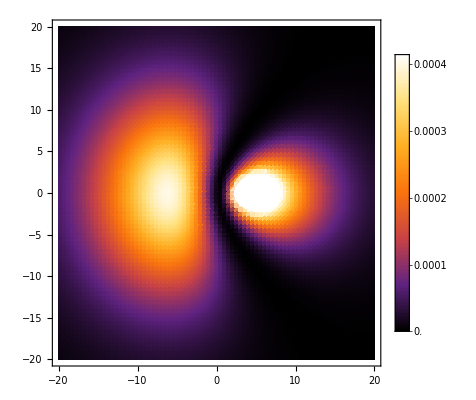

```mathematica
DensityPlot[Abs[ψ2Norm[x,y,0]]^2,{x,-20,20},{y,-20,20},PlotPoints->80,ColorFunction->"SunsetColors",PlotLegends->Automatic,Exclusions->None]
```

```mathematica
ψbondXY[x_,y_,z_]:=ψ1[x,y,z]+ψ2[x,y,z]
```

```mathematica
normalizationb=NIntegrate[Abs[ψbondXY[x,y,z]]^2,{x,-10,10},{y,-10,10},{z,-10,10},Method->"AdaptiveMonteCarlo",AccuracyGoal->3,PrecisionGoal->3]
```

0.393697

```mathematica
(*Correct normalization*)
ψbondXYNorm[x_,y_,z_]:=ψbondXY[x,y,z]/Sqrt[normalizationb]

(*Now check normalization*)
NIntegrate[Abs[ψ2Norm[x,y,z]]^2,{x,-10,10},{y,-10,10},{z,-10,10},Method->"AdaptiveMonteCarlo",AccuracyGoal->3,PrecisionGoal->3]
```

0.998482

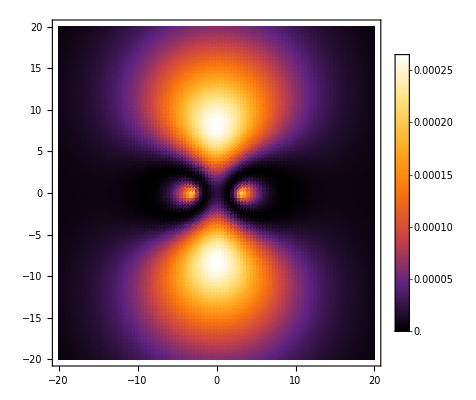

```mathematica
DensityPlot[Abs[ψbondXYNorm[x,y,0]]^2,{x,-20,20},{y,-20,20},PlotPoints->100,ColorFunction->"SunsetColors",PlotLegends->Automatic,Exclusions->None]
```

```mathematica
(*Exclusions->None was important because i was getting white horizontal lines*)
```

```mathematica
(*i can also plot the pi bonds but we can od it later*)
```

(**)
The most important orbital for tight - binding calculations in graphene is the 2 p_z orbital of each carbon atom . These orbitals form the π - bands, which dominate the electronic properties near the Fermi level .
   
   Tight - Binding MINIMAL MODEL

Nearest - Neighbor Approximation : The simplest and most common tight - binding model for graphene considers only the 2 p_z orbitals and nearest - neighbor hopping . The hopping parameter (t) between adjacent carbon atoms is typically around 2.7–3.0 eV .
   
   Further Neighbors : For more accuracy, you can include second - or third - nearest - neighbor hopping, but these terms are smaller (e . g ., t' ≈ 0.1–0.3 eV for second - nearest neighbors) and often neglected in introductory models .
    
    On - Site Energy : The on - site energy for the 2 p_z orbitals is usually set to zero (as the reference energy) for simplicity, assuming no external potential .
    
    Step 1 — Set up the honeycomb lattice and nearest-neighbour vectors
    
    
    
    For graphene we keep one 2pz orbital per carbon



Doing a Fourier transform so we can work in k space



so we are working with the two wave functions of two carbon atoms where we are assuming that pz is the wave function. We have a 2x2 matrix.
Diagonal elements:



if  A is at R and B is at R+delta


so here is better to write the integrals by hand, but after this is notable that the integral is the spatial overlapping between the wave functions, and the exponentials are the sum of the B neighbors

​

    
    t = nearest-neighbour π-hopping



        where  is the crystal Hamiltonian and are  the out-of-plane  orbitals on two adjacent carbon atoms.
        ​


with nearest neighboors

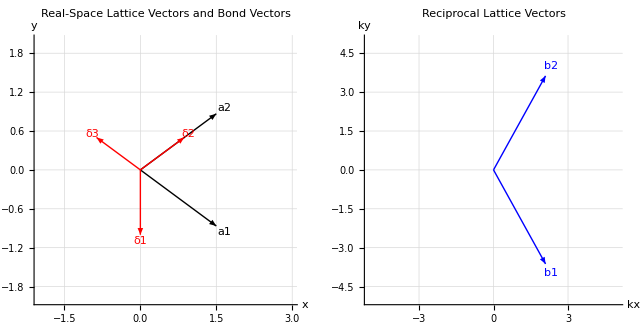

```mathematica
(*Lattice constant*)a=1;

(*Real-space lattice vectors*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};

(*Compute area of unit cell*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];

(*Reciprocal lattice vectors*)
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};

(*Bond (delta) vectors*)
delta1=a*{0,-1};
delta2=a*{Sqrt[3]/2,1/2};
delta3=a*{-Sqrt[3]/2,1/2};
deltas={delta1,delta2,delta3};

(*----Plot Real Space Vectors----*)
realVectors=Graphics[{(*Plot lattice vectors*)Arrow[{{0,0},a1}],Text["a1",1.1*a1,{0,-1}],Arrow[{{0,0},a2}],Text["a2",1.1*a2,{0,1}],(*Plot delta vectors*)Red,Arrow[{{0,0},delta1}],Text["δ1",1.1*delta1,{-1,0}],Arrow[{{0,0},delta2}],Text["δ2",1.1*delta2,{1,0}],Arrow[{{0,0},delta3}],Text["δ3",1.1*delta3,{-1,0}]},Axes->True,AxesLabel->{"x","y"},PlotRange->{{-2,3},{-2,2}},GridLines->Automatic,AspectRatio->1,PlotLabel->"Real-Space Lattice Vectors and Bond Vectors"];

(*----Plot Reciprocal Space Vectors----*)
reciprocalVectors=Graphics[{Blue,Arrow[{{0,0},b1}],Text["b1",1.1*b1,{0,-1}],Arrow[{{0,0},b2}],Text["b2",1.1*b2,{0,1}]},Axes->True,AxesLabel->{"kx","ky"},PlotRange->{{-5,5},{-5,5}},GridLines->Automatic,AspectRatio->1,PlotLabel->"Reciprocal Lattice Vectors"];

(*Show plots side by side*)
GraphicsRow[{realVectors,reciprocalVectors}]
```

```mathematica
Quit
```

```mathematica
(*---Lattice vectors---*)
a=2.46; (*lattice constant,set to 1 for simplicity*)

a1={3/2,-Sqrt[3]/2}*a
a2={3/2,Sqrt[3]/2}*a
(*here is important the coordinate system

     C
  \
 delta 2
     \   
      C - delta1 - C
     /
delta 3  
  / 
 C
*)
```

{3.69,-2.13042}

{3.69,2.13042}

```mathematica
(*Compute unit cell area (2D cross product)*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]]

(*Compute reciprocal lattice vectors*)
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]}
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]}
```

15.7225

{0.85138,-1.47463}

{0.85138,1.47463}

```mathematica
delta1=(a1+a2)/3;
delta2=(-2*a1/3+a2/3);
delta3=(a1/3-2*a2/3);
deltas={delta1,delta2,delta3};
```

```mathematica
(*---Gamma(k) function---*)
gamma[kx_,ky_]:=Total[Exp[I (kx #1[[1]]+ky #1[[2]])]&/@deltas]

(*---Energy bands:±t|γ(k)|---*)
t=2.7; (*hopping parameter*)
Ek[kx_,ky_]:=±t Abs[gamma[kx,ky]]
```

```mathematica
(*x-axis show the actual distance traveled in k-space as you move from Γ->K->M->Γ.That’s how band structure plots in papers often show the horizontal axis.*)
```

```mathematica
kΓ={0,0};
kK=(1/3)*(b1-b2);
kM=(1/2)*b1;


kPath=Join[Table[(1-s) kΓ+s kK,{s,0,1,0.01}],Table[(1-s) kK+s kM,{s,0,1,0.01}],Table[(1-s) kM+s kΓ,{s,0,1,0.01}]];
```

```mathematica
kDistances=
Prepend[
Accumulate[
Norm/@Differences[kPath]
],
0
];
```

```mathematica
bands=Table[
{
kDistances[[i]],
t Abs[gamma@@kPath[[i]]],
-t Abs[gamma@@kPath[[i]]]},
{i,Length[kPath]}
];
```

```mathematica
symmetryPoints={1,101,202,303};
tickPositions=kDistances[[symmetryPoints]];
tickLabels={"Γ","K","M","Γ"};
ticks=Transpose[{tickPositions,tickLabels}];
```

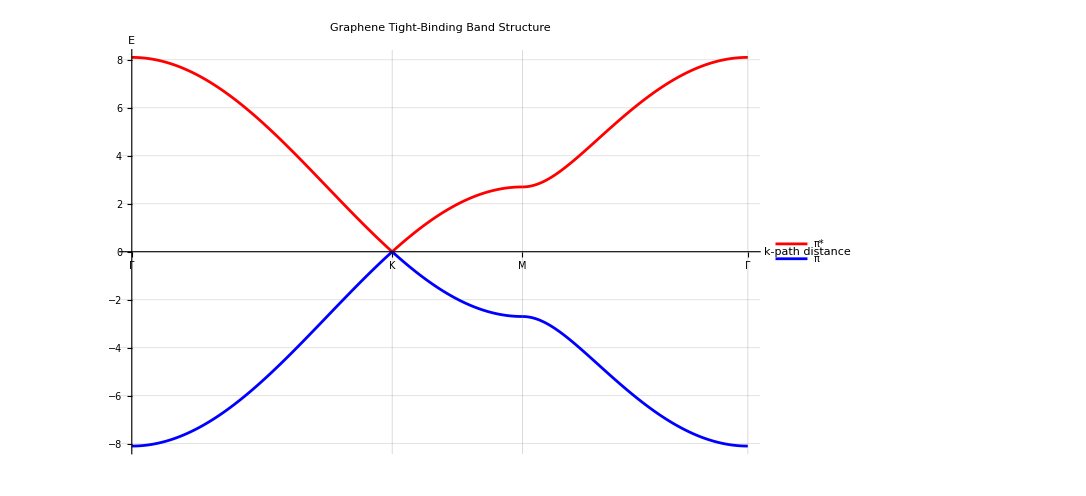

```mathematica
ListLinePlot[
{
bands[[All,{1,2}]],
bands[[All,{1,3}]]
},
PlotRange->All,
PlotStyle->{Red,Blue},
AxesLabel->{"k-path distance","E"},
PlotLegends->{"π*","π"},
Ticks->{ticks,Automatic},
GridLines->Automatic,
PlotLabel->"Graphene Tight-Binding Band Structure"
]
```

```mathematica
Quit
```